```mathematica
SetDirectory[NotebookDirectory[]]
<<OperatorGB.m
```

/Users/clemenshofstadler/Desktop/OperatorGB

Package OperatorGB version 1.0.1
Copyright 2019, Institute of Algebra, JKU
written by Clemens Hofstadler

A few definitions need to be made by the user. Type ?SetUpRing for more information.

### Small example from the slides

```mathematica
SetUpRing[{a,b,am,bm,i}];
```

a < b < am < bm < i

```mathematica
Q ={{a,2,1},{am,1,2},{i,2,2},{b,3,2},{bm,2,3}};
```

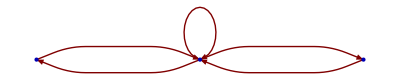

```mathematica
PlotQuiver[Q]
```

```mathematica
assumptions = {a**am**a-a,
		b**bm**b-b,
		b**bm**i-b**bm**am**a-i+am**a,-i**b-b};
claim = a**b**bm**am**a**b-a**b;
```

```mathematica
QSignature[#,Q]&/@assumptions
```

{{{2,1}},{{3,2}},{{2,2}},{{3,2}}}

```mathematica
cofactors = {};
```

```mathematica
G = Groebner[cofactors,assumptions,Info->True,Parallel->False];
```

G has 4 elements in the beginning.

6 ambiguities in total (computation took 0.000986)

Generating S-polys: 0.000645 (4 in total)

Reducing S-polys: 0.000415 (2 remaining)

The second reduction took 0.231811

Iteration 1 finished. G has now 6 elements

5 ambiguities in total (computation took 0.00092)

Generating S-polys: 0.000647 (5 in total)

Reducing S-polys: 0.000658 (3 remaining)

The second reduction took 0.148829

Iteration 2 finished. G has now 8 elements

10 ambiguities in total (computation took 0.001053)

Generating S-polys: 0.000936 (8 in total)

Reducing S-polys: 0.000757 (0 remaining)

Rewriting the cofactors has started.

Rewriting the cofactors took in total 0.164635

```mathematica
ReducedForm[vars,G,claim]
```

0

```mathematica
( Rewrite[vars,cofactors]//MultiplyOut)===claim
```

True

```mathematica
(*only linear combination in terms of monic versions of generators*) 
Rewrite[vars,cofactors]/.Map[{_,#,_}->Nothing&,assumptions]
Rewrite[vars,cofactors]/.Map[{_,#/LeadingTerm[#][[1]],_}->Nothing&,assumptions]
```

{{a,i-am**a-b**bm**i+b**bm**am**a,b},{-a,b+i**b,1},{a**b**bm,b+i**b,1}}

{}

```mathematica
(*now we do all at once - and get linear combination in terms of generators and not their monic versions*)
```

```mathematica
certificate =Certify[assumptions,claim,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < am < i < b < bm

Interreduced the input from 4 polynomials to 4.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 4 elements in the beginning.

6 ambiguities in total (computation took 0.003547)

Removed 0 ambiguities in 0.000166

Generating S-polys: 0.005635 (4 in total)

Reducing S-polys: 0.000404 (2 remaining)

The second reduction took 0.196169

Iteration 1 finished. G has now 6 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.113759

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut[certificate[[4]]]===claim
```

True

```mathematica
certificate[[4]]/.Map[{__,#,__}->Nothing&,assumptions]
```

{}

### Hartwig (small version)

```mathematica
Q = {{a,3,4},{adj[a],4,3},
{b,2,3},{adj[b],3,2},
{c,1,2},{adj[c],2,1},
{aa,4,3},{adj[aa],3,4},
{bb,3,2},{adj[bb],2,3},
{cc,2,1},{adj[cc],1,2},
{m,1,4},{adj[m],4,1},
{mm,4,1},{adj[mm],1,4}};
```

```mathematica
PinvA = {a**aa**a-a,aa**a**aa- aa,adj[aa]**adj[a]-a**aa,adj[a]**adj[aa]-aa**a};
PinvB = {b**bb**b-b,bb**b**bb- bb,adj[bb]**adj[b]-b**bb,adj[b]**adj[bb]-bb**b};
PinvC = {c**cc**c-c,cc**c**cc- cc,adj[cc]**adj[c]-c**cc,adj[c]**adj[cc]-cc**c};
PinvM = {m**mm**m-m,mm**m**mm- mm,adj[mm]**adj[m]-m**mm,adj[m]**adj[mm]-mm**m};
MatP =  aa**a**b**c**cc;
MatQ = c**cc**bb**aa**a;
DefM = {m-a**b**c,mm-cc**bb**aa};
cond2 = {MatQ**MatP**MatQ-MatQ,MatP**MatQ**MatP-MatP,
	MatQ**MatP**c**adj[c]-adj[MatQ**MatP**c**adj[c]],
	adj[a]**a**MatP**MatQ-adj[adj[a]**a**MatP**MatQ]};
cond3 = {MatP**MatQ**MatP-MatP, MatQ**MatP**MatQ-MatQ,
	MatQ**MatP**c**adj[c]**adj[MatP]-c**adj[c]**adj[MatP],adj[MatQ]**adj[MatP]**adj[a]**a**MatP-adj[a]**a**MatP};
cond4 = {MatP**MatQ**MatP**MatQ-MatP**MatQ,
MatQ**MatP**MatQ-MatQ,MatQ**MatP**c**adj[c]**adj[MatP]-c**adj[c]**adj[MatP],
adj[MatQ]**adj[MatP]**adj[a]**a**MatP - adj[a]**a**MatP};
AddAdj[S_List] := Join[S,adj/@S];
```

(i) => (ii):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,DefM,PinvM]// AddAdj;
```

```mathematica
certificate = Certify[assumptions,cond2,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

52 ambiguities in total (computation took 0.028841)

Removed 0 ambiguities in 0.002823

Generating S-polys: 0.018836 (44 in total)

Reducing S-polys: 0.002916 (12 remaining)

The second reduction took 0.185503

Iteration 1 finished. G has now 40 elements

Starting iteration 2...

G has 40 elements in the beginning.

48 ambiguities in total (computation took 0.049018)

Removed 0 ambiguities in 0.003256

Generating S-polys: 0.021362 (42 in total)

Reducing S-polys: 0.004532 (26 remaining)

The second reduction took 0.145999

Iteration 1 finished. G has now 56 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.186754

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond2
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(ii) => (i):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,DefM,cond2]// AddAdj;
```

```mathematica
certificate = Certify[assumptions,PinvM,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 36 polynomials to 29.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 29 elements in the beginning.

98 ambiguities in total (computation took 0.036221)

Removed 17 ambiguities in 0.005747

Generating S-polys: 0.042345 (72 in total)

Reducing S-polys: 0.008717 (43 remaining)

The second reduction took 0.166125

Iteration 1 finished. G has now 68 elements

Starting iteration 2...

G has 68 elements in the beginning.

373 ambiguities in total (computation took 0.151801)

Removed 86 ambiguities in 0.042371

Generating S-polys: 0.115472 (277 in total)

Reducing S-polys: 0.047016 (134 remaining)

The second reduction took 0.231003

Iteration 1 finished. G has now 139 elements

Starting iteration 3...

G has 139 elements in the beginning.

1582 ambiguities in total (computation took 0.364258)

Removed 700 ambiguities in 0.385339

Generating S-polys: 0.287254 (788 in total)

Reducing S-polys: 0.153438 (167 remaining)

The second reduction took 0.144519

Iteration 1 finished. G has now 188 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.26306

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===PinvM
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(ii) => (iii):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,cond2]// AddAdj;
certificate = Certify[assumptions,cond3,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 32 polynomials to 25.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 25 elements in the beginning.

88 ambiguities in total (computation took 0.030378)

Removed 19 ambiguities in 0.003884

Generating S-polys: 0.044163 (57 in total)

Reducing S-polys: 0.008093 (24 remaining)

The second reduction took 0.157069

Iteration 1 finished. G has now 48 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.123938

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond3
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(iii) => (ii)

```mathematica
ideal = Join[PinvA,PinvB,PinvC,cond3]// AddAdj;
certificate = Certify[assumptions,cond2,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 32 polynomials to 25.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 25 elements in the beginning.

88 ambiguities in total (computation took 0.030088)

Removed 19 ambiguities in 0.004431

Generating S-polys: 0.042897 (57 in total)

Reducing S-polys: 0.008256 (24 remaining)

The second reduction took 0.161856

Iteration 1 finished. G has now 48 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.191897

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond2
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(ii) => (iv):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,cond2]// AddAdj;
certificate = Certify[assumptions,cond4,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 32 polynomials to 25.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 25 elements in the beginning.

88 ambiguities in total (computation took 0.028387)

Removed 19 ambiguities in 0.003734

Generating S-polys: 0.043374 (57 in total)

Reducing S-polys: 0.008298 (24 remaining)

The second reduction took 0.110699

Iteration 1 finished. G has now 48 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.121763

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond4
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(iv) => (ii):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,cond4]// AddAdj;
certificate = Certify[assumptions,cond2,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 32 polynomials to 24.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 24 elements in the beginning.

79 ambiguities in total (computation took 0.026533)

Removed 10 ambiguities in 0.003851

Generating S-polys: 0.044919 (57 in total)

Reducing S-polys: 0.008041 (28 remaining)

The second reduction took 0.11089

Iteration 1 finished. G has now 49 elements

Starting iteration 2...

G has 49 elements in the beginning.

542 ambiguities in total (computation took 0.134661)

Removed 286 ambiguities in 0.048142

Generating S-polys: 0.153239 (203 in total)

Reducing S-polys: 0.045818 (105 remaining)

The second reduction took 0.093921

Iteration 1 finished. G has now 87 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.163207

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond2
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(iii) => (iv):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,cond3]// AddAdj;
certificate = Certify[assumptions,cond4,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 32 polynomials to 26.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 26 elements in the beginning.

105 ambiguities in total (computation took 0.033634)

Removed 18 ambiguities in 0.004971

Generating S-polys: 0.054738 (70 in total)

Reducing S-polys: 0.010581 (36 remaining)

The second reduction took 0.132709

Iteration 1 finished. G has now 59 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.118113

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond4
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(iv) => (iii):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,cond4]// AddAdj;
certificate = Certify[assumptions,cond3,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 32 polynomials to 24.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 24 elements in the beginning.

79 ambiguities in total (computation took 0.026471)

Removed 10 ambiguities in 0.00479

Generating S-polys: 0.045015 (57 in total)

Reducing S-polys: 0.008311 (28 remaining)

The second reduction took 0.103204

Iteration 1 finished. G has now 49 elements

Starting iteration 2...

G has 49 elements in the beginning.

542 ambiguities in total (computation took 0.136972)

Removed 286 ambiguities in 0.049887

Generating S-polys: 0.162197 (203 in total)

Reducing S-polys: 0.045555 (105 remaining)

The second reduction took 0.09941

Iteration 1 finished. G has now 87 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.115395

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond3
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(i) => (iii):

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,DefM,PinvM]// AddAdj;
certificate = Certify[assumptions,cond3,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

52 ambiguities in total (computation took 0.027481)

Removed 0 ambiguities in 0.003662

Generating S-polys: 0.029771 (44 in total)

Reducing S-polys: 0.002943 (12 remaining)

The second reduction took 0.121295

Iteration 1 finished. G has now 40 elements

Starting iteration 2...

G has 40 elements in the beginning.

48 ambiguities in total (computation took 0.051051)

Removed 0 ambiguities in 0.003427

Generating S-polys: 0.032346 (42 in total)

Reducing S-polys: 0.004396 (26 remaining)

The second reduction took 0.105814

Iteration 1 finished. G has now 56 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.139377

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond3
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(i) => (iv)

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,DefM,PinvM]// AddAdj;
certificate = Certify[assumptions,cond4,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

52 ambiguities in total (computation took 0.026909)

Removed 0 ambiguities in 0.002882

Generating S-polys: 0.029163 (44 in total)

Reducing S-polys: 0.002983 (12 remaining)

The second reduction took 0.126893

Iteration 1 finished. G has now 40 elements

Starting iteration 2...

G has 40 elements in the beginning.

48 ambiguities in total (computation took 0.05001)

Removed 0 ambiguities in 0.003154

Generating S-polys: 0.032267 (42 in total)

Reducing S-polys: 0.006002 (26 remaining)

The second reduction took 0.139104

Iteration 1 finished. G has now 56 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.138219

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond4
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(iv) => (i)

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,DefM,cond4]// AddAdj;
certificate = Certify[assumptions,PinvM,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 36 polynomials to 29.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 29 elements in the beginning.

94 ambiguities in total (computation took 0.037226)

Removed 14 ambiguities in 0.00534

Generating S-polys: 0.042911 (70 in total)

Reducing S-polys: 0.007289 (42 remaining)

The second reduction took 0.148392

Iteration 1 finished. G has now 66 elements

Starting iteration 2...

G has 66 elements in the beginning.

362 ambiguities in total (computation took 0.143619)

Removed 80 ambiguities in 0.04348

Generating S-polys: 0.115432 (259 in total)

Reducing S-polys: 0.038609 (119 remaining)

The second reduction took 0.14484

Iteration 1 finished. G has now 118 elements

Starting iteration 3...

G has 118 elements in the beginning.

1092 ambiguities in total (computation took 0.261302)

Removed 510 ambiguities in 0.214786

Generating S-polys: 0.197933 (528 in total)

Reducing S-polys: 0.084942 (79 remaining)

The second reduction took 0.124325

Iteration 1 finished. G has now 156 elements

Starting iteration 4...

G has 156 elements in the beginning.

1292 ambiguities in total (computation took 0.23966)

Removed 839 ambiguities in 0.267367

Generating S-polys: 0.15592 (385 in total)

Reducing S-polys: 0.07788 (38 remaining)

The second reduction took 0.12178

Iteration 1 finished. G has now 172 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.207054

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===PinvM
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

(iii) => (i)

```mathematica
assumptions = Join[PinvA,PinvB,PinvC,DefM,cond3]// AddAdj;
certificate = Certify[assumptions,PinvM,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < aa < adj[aa] < bb < adj[bb] < cc < adj[cc] < m < adj[m] < mm < adj[mm]

Interreduced the input from 36 polynomials to 30.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 30 elements in the beginning.

105 ambiguities in total (computation took 0.039314)

Removed 17 ambiguities in 0.006038

Generating S-polys: 0.046036 (76 in total)

Reducing S-polys: 0.008925 (48 remaining)

The second reduction took 0.153961

Iteration 1 finished. G has now 72 elements

Starting iteration 2...

G has 72 elements in the beginning.

431 ambiguities in total (computation took 0.15692)

Removed 103 ambiguities in 0.054102

Generating S-polys: 0.125963 (300 in total)

Reducing S-polys: 0.046889 (126 remaining)

The second reduction took 0.117354

Iteration 1 finished. G has now 135 elements

Starting iteration 3...

G has 135 elements in the beginning.

1484 ambiguities in total (computation took 0.348302)

Removed 786 ambiguities in 0.329646

Generating S-polys: 0.229167 (607 in total)

Reducing S-polys: 0.10522 (80 remaining)

The second reduction took 0.136181

Iteration 1 finished. G has now 172 elements

Starting iteration 4...

G has 172 elements in the beginning.

1363 ambiguities in total (computation took 0.276962)

Removed 905 ambiguities in 0.311794

Generating S-polys: 0.162615 (393 in total)

Reducing S-polys: 0.08794 (36 remaining)

The second reduction took 0.097799

Iteration 1 finished. G has now 186 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.217319

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===PinvM
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### General inverses

```mathematica
Q= {{p,1,1},{q,1,1},{a,1,2},{g[a],2,1},{b,2,1},{g[b],1,2}};
```

```mathematica
ginvA = {-a+a**g[a]**a,-g[a]+g[a]**a**g[a]};
ginvB = {-b+b**g[b]**b,-g[b]+g[b]**b**g[b]};
ROL = {-a**b+a**b**g[b]**g[a]**a**b,-g[b]**g[a]+g[b]**g[a]**a**b**g[b]**g[a]};
proj = {p-g[a]**a,q-b**g[b]};
additionalCondition = {p**q-q**p};
assumptions = Join[ginvA,ginvB,proj,additionalCondition];
```

```mathematica
certificate = Certify[assumptions,ROL,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

p < q < a < g[a] < b < g[b]

Interreduced the input from 7 polynomials to 7.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 7 elements in the beginning.

8 ambiguities in total (computation took 0.003909)

Removed 0 ambiguities in 0.00022

Generating S-polys: 0.018347 (6 in total)

Reducing S-polys: 0.00043 (6 remaining)

The second reduction took 0.195586

Iteration 1 finished. G has now 11 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.117768

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===ROL
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{}}

### Inner Inverses

```mathematica
Q= {{a,1,2},{aa,2,1},{b,2,1},{bb,1,2},{i,1,1}};
```

```mathematica
innerinv = {-a+a**aa**a,-b+b**bb**b};
cond = {-i+aa**a+b**bb**i-b**bb**aa**a};
prop = {-i+i**i,a**i-a,-aa+i**aa,-b+i**b,-bb+bb**i};
claim =-a**b+a**b**bb**aa**a**b;
```

```mathematica
assumptions = Join[innerinv,cond,prop];
```

```mathematica
certificate = Certify[assumptions,claim,Q,Info->True];
```

Using the following monomial ordering:

a < aa < b < bb < i

Interreduced the input from 8 polynomials to 8.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 8 elements in the beginning.

17 ambiguities in total (computation took 0.005055)

Removed 0 ambiguities in 0.000443

Generating S-polys: 0.007412 (6 in total)

Reducing S-polys: 0.000451 (0 remaining)

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.232499

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut[certificate[[4]]]===claim
certificate[[4]]/.Map[{_,#,_}->Nothing&,assumptions]
```

True

{}

### Moore-Penrose inverse is unique

```mathematica
Q = {{a,A,B},{adj[a],B,A},{aa,B,A},{adj[aa],A,B},{bb,B,A},{adj[bb],A,B}};
PinvA1 = {a**aa**a-a,aa**a**aa- aa,adj[aa]**adj[a]-a**aa,adj[a]**adj[aa]-aa**a};
PinvA2 = {a**bb**a-a,bb**a**bb- bb,adj[bb]**adj[a]-a**bb,adj[a]**adj[bb]-bb**a};
AddAdj[S_List] := Join[S,adj/@S];
assumptions= Join[PinvA1,PinvA2]//AddAdj;
```

```mathematica
certificate  = Certify[assumptions,aa-bb,Q,MultiLex->False,Criterion->True,Info->True];
```

Using the following monomial ordering:

a < adj[a] < aa < adj[aa] < bb < adj[bb]

Interreduced the input from 16 polynomials to 12.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 12 elements in the beginning.

28 ambiguities in total (computation took 0.010243)

Removed 0 ambiguities in 0.000805

Generating S-polys: 0.010626 (24 in total)

Reducing S-polys: 0.001661 (8 remaining)

The second reduction took 0.189907

Iteration 1 finished. G has now 18 elements

Starting iteration 2...

G has 18 elements in the beginning.

28 ambiguities in total (computation took 0.023999)

Removed 2 ambiguities in 0.001145

Generating S-polys: 0.010984 (24 in total)

Reducing S-polys: 0.002313 (9 remaining)

The second reduction took 0.179083

Iteration 1 finished. G has now 23 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.137075

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
certificate[[4]]//MultiplyOut
certificate[[4]]/.Map[{_,#,_}->Nothing&,assumptions]
```

aa-bb

{}

### Moore-Penrose inverse and singular value decomposition (does not work)

```mathematica
A = {u**Σ**vInv};
PinvA = {a**aa**a-a,aa**a**aa- aa,adj[aa]**adj[a]-a**aa,adj[a]**adj[aa]-aa**a};
U = {u**uInv - iu, uInv**u-iu,iu**iu-iu,adj[u]-uInv};
V = {v**vInv - iv, vInv**v-iv,iv**iv-iv,adj[v]-vInv};
PinvSigma ={a**aa**a-a,aa**a**aa- aa,adj[aa]**adj[a]-a**aa,adj[a]**adj[aa]-aa**a}/.{a->Σ,aa->ΣΣ};
AddAdj[S_List] := Join[S,adj/@S];
assumptions = Join[A,PinvA,U,V,PinvSigma]//AddAdj;
claim = aa-v**ΣΣ**uInv;

SetUpRing[{a,adj[a],aa,adj[aa],u,adj[u],uInv,adj[uInv],v,adj[v],vInv,adj[vInv],iu,adj[iu],iv,adj[iv],Σ,adj[Σ],ΣΣ,adj[ΣΣ]}]
```

a < adj[a] < aa < adj[aa] < u < adj[u] < uInv < adj[uInv] < v < adj[v] < vInv < adj[vInv] < iu < adj[iu] < iv < adj[iv] < Σ < adj[Σ] < ΣΣ < adj[ΣΣ]

```mathematica
red = Interreduce[assumptions][[1]];
```

```mathematica
cofactors = {};
G = Groebner[cofactors,red,20,Info->False];
ReducedForm[vars,G,claim]
```

aa-v**ΣΣ**adj[u]

### Some small lemma (adj[A]A = 0 => A = 0)

```mathematica
PinvA = {a**aa**a-a,aa**a**aa- aa,adj[aa]**adj[a]-a**aa,adj[a]**adj[aa]-aa**a};
```

```mathematica
AddAdj[S_List] := Join[S,adj/@S];
assumptions = Join[PinvA,{adj[a]**a}]//AddAdj;
```

```mathematica
Interreduce[assumptions][[1]](*first element is claim*)
```

{Prod[a],Prod[aa],Prod[adj[a]],Prod[adj[aa]],Prod[adj[a],a]}

```mathematica
Q = {{a,X,Y},{adj[a],Y,X},{aa,Y,X},{adj[aa],X,Y}};
```

```mathematica
certificate  = Certify[assumptions,a,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < aa < adj[aa]

Interreduced the input from 10 polynomials to 5.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 5 elements in the beginning.

2 ambiguities in total (computation took 0.009456)

Removed 1 ambiguities in 0.000061

Generating S-polys: 0.006525 (0 in total)

Reducing S-polys: 0.000039 (0 remaining)

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.220074

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

### Woodbury matrix inversion identity

```mathematica
A = a+u**c**v;
InvA = inva-inva**u**invs**v**inva;
s = invc+ v**inva**u;
```

```mathematica
InverseA = {a**inva - ia, inva**a-ia};
InverseC = {c**invc - ic, invc**c-ic};
InverseS = {s**invs-ic,invs**s-ic};
Id = {a**ia-a,ia**a-a,ia**ia-ia,c**ic-c,ic**c-c,ic**ic-ic,A**ia -A,ia**A-A,inva**ia-inva,ia**inva-inva,invc**ic-invc,ic**invc-invc,InvA**ia-InvA,ia**InvA-InvA,s**ic-s,ic**s-ic,invs**ic-invs,ic**invs-invs};

assumptions = Distribute/@Join[InverseA,InverseC,InverseS,Id];
claims = Distribute/@{A**InvA-ia,InvA**A-ia};
```

```mathematica
Q = {{a,1,1},{inva,1,1},{u,2,1},{v,1,2},{c,2,2},{invc,2,2},{invs,2,2},{ia,1,1},{ic,2,2}};
```

```mathematica
certificate =  Certify[assumptions,claims,Q,Info->True];
```

Using the following monomial ordering:

a < inva < u < v < c < invc < invs < ia < ic

Interreduced the input from 24 polynomials to 22.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 22 elements in the beginning.

70 ambiguities in total (computation took 0.0165)

Removed 0 ambiguities in 0.002889

Generating S-polys: 0.028094 (34 in total)

Reducing S-polys: 0.00231 (9 remaining)

The second reduction took 0.154519

Iteration 1 finished. G has now 26 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.16621

Rewriting the linear combination in terms of the assumptions has started...

Done! All claims were successfully reduced to 0.

```mathematica
(*our results are always expanded but NonCommutativeMultiply can not expand terms automatically 
*)
MultiplyOut/@certificate[[4]]===ToNonCommutativeMultiply/@ToProd/@claims
```

True

```mathematica
certificate[[4]]/.Map[{_,ToNonCommutativeMultiply[ToProd[#]],_}->Nothing&,assumptions]
```

{{},{}}